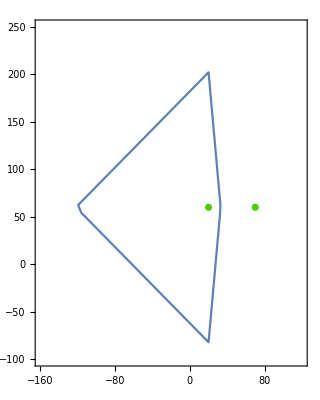

D:\study\phd_research\main\horsefly\viz_aid

D:\study\phd_research\main\horsefly\viz_aid\2drones_L1_1.pdf

```mathematica
ClearAll["Global`*"]
xx={20, 70};
yy ={60,60};
data=Transpose@{xx,yy};
plot1= ListPlot[data, PlotStyle->{RGBColor[0.3,0.8,0]}];
plot2= ContourPlot[
{(1/10) (Abs[x-20]+Abs[y-60])-(1/12)(Abs[x-70]+Abs[y-60])+1.8==0},
{x,-160,120},{y,-100,250}];
s = Show[{plot2, plot1}, AspectRatio->Automatic]
SetDirectory["D:\study\phd_research\main\horsefly\viz_aid"]
Export[Directory[] <> "\2drones_L1_1.pdf",s]
```

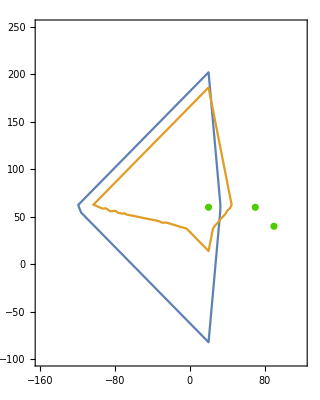

D:\study\phd_research\main\horsefly\viz_aid

Export::noopen: Cannot open D:\study\phd_research\main\horsefly\viz_aid\3drones_L1_1.pdf.

$Failed

```mathematica
ClearAll["Global`*"]
xx={20, 70, 90};
yy ={60,60,40};
data=Transpose@{xx,yy};
plot1= ListPlot[data, PlotStyle->{RGBColor[0.3,0.8,0]}];
plot2= ContourPlot[
{(1/10) (Abs[x-20]+Abs[y-60])-(1/12)(Abs[x-70]+Abs[y-60])+1.8==0,
(1/10)  (Abs[x-20]+Abs[y-60])-(1/15)(Abs[x-90]+Abs[y-40])+1.8==0},
{x,-160,120},{y,-100,250}];
s = Show[{plot2, plot1}, AspectRatio->Automatic]
SetDirectory["D:\study\phd_research\main\horsefly\viz_aid"]
Export[Directory[] <> "\3drones_L1_1.pdf",s]
```

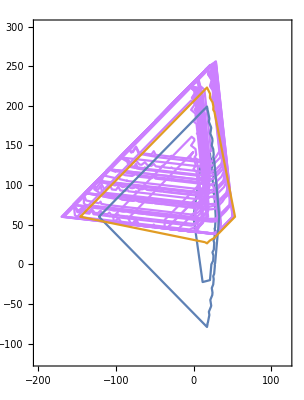

D:\study\phd_research\main\horsefly\viz_aid\3drones_L1_center.pdf

```mathematica
ClearAll["Global`*"]
xx={20, 70, 90};
yy ={60,60,20};
v0 = 10;
v1 = 12;
v2=  15;
data=Transpose@{xx,yy};
plot1= ListPlot[data, PlotStyle->{RGBColor[0.3,0.8,0]}];
plot2 = ContourPlot[(1/10)(  Abs[x-20]2+Abs[y-60])-(1/12)(Abs[x-70]+Abs[y-60])+1.8==0,{x,-200,120},{y,-120,300}];
plot3= ContourPlot[
{(1/10) (Abs[x-20]+Abs[y-60])-(1/12)(Abs[x-70]+Abs[y-60])+1.8==0,
(1/10)  (Abs[x-20]+Abs[y-60])-(1/15)(Abs[x-90]+Abs[y-20])+1.8==0},
{x,-200,120},{y,-120,300}];
points=Cases[Normal@plot2,Line[pts_]->pts,Infinity];
Join@@points;(*if you don't want disjoint components to be separate*)
points = points[[1]];
t0 = 1.8;

plotList = {};
Do[
xq = i[[1]];
yq= i[[2]];
ploti=ContourPlot[
(1/v1)(Abs[xq-70]+Abs[yq-60])+
(1/v1)(Abs[x-xq]+Abs[y-yq])-
(1/v2)(Abs[x-90]+Abs[y-20])
==0,
{x,-200,120},{y,-120,300}, ContourStyle->RGBColor[0.8,0.5,1]];
AppendTo[plotList,ploti];
,{i, points}]
PrependTo[plotList,plot2];
AppendTo[plotList,plot3];
s = Show[plotList, AspectRatio->Automatic]
Export[Directory[] <> "\3drones_L1_center.pdf",s]
```

```mathematica
Plot3D[(1/1.5)(Abs[x-1]+Abs[y-1])+(1/1.5)(Abs[x-2]+Abs[y-4]),{x,-4,8},{y,-5,10},ColorFunction->"RustTones"]
```

-Graphics3D-

```mathematica
s = Show[
Plot3D[{(1/10)  (Abs[x-20]+Abs[y-60])-(1/15)(Abs[x-90]+Abs[y-40])+1.8},{x,-160,120},{y,-100,250},ColorFunction->Function[{x,y,z},Hue[.65(1-z)]], PlotPoints->150,MaxRecursion->8],
 Plot3D[z=0,{x,-160,120},{y,-100,250},ColorFunction->Function[{x,y,z},RGBColor[1,0.5,0.5]],
 PlotPoints->150,MaxRecursion->8],
ListPointPlot3D[{{0,80,0.5},{20,60,0.5},{90,40,11}}, PlotStyle->RGBColor[0,0,1]],
 AspectRatio->Automatic]
```

-Graphics3D-